```mathematica
<<VariationalMethods`
```

### Introducing Lagrange’s equation:

```mathematica
(*Introducing Kinetic energy 'T' and potential energy 'U' for N atoms*)
T[t_,N_]:=1/2(∑_(l=1)^N (Subscript[x, l]'[t])^2)
U[t_,N_]:=1/2 Subscript[ω, 0]^2((Subscript[x, 1][t])^2+(Subscript[x, N][t])^2+∑_(i=2)^N (Subscript[x, i][t]-Subscript[x, i-1][t])^2)
```

```mathematica
(* Defining the Lagrangian to be L = T - U*)
L[N_]:=T[t,N]-U[t,N]
```

```mathematica
(* Using mathematica to apply Euler's equation on 'L' to find the equations of motion*)
EoM[N_,j_]:=EulerEquations[L[N], Subscript[x,j][t],t]
```

```mathematica
(* Showing the equation of motion for the first, middle, and the last atom for a system of 3 atoms*)
```

```mathematica
Expand@EoM[3,1]//TraditionalForm (* the equation of motion of the first atom*)
```

-x_1''(t)-2 x_1(t)+x_2(t)==0

```mathematica
Expand@EoM[3,2]//TraditionalForm(* the equation of motion of the middle atom*)
```

-x_2''(t)+x_1(t)-2 x_2(t)+x_3(t)==0

```mathematica
Expand@EoM[3,3]//TraditionalForm(* the equation of motion of a final atom*)
```

-x_3''(t)+x_2(t)-2 x_3(t)==0

### Constructing the matrix D_n and evaluating its eigenmodes:

```mathematica
(* Intorducing Dn, the matrix of the coefficients of the equations of motion*)
Dn[N_]:=Table[Coefficient[-Subscript[ω, 0]^2 (Subscript[x, i-1][t]-2 Subscript[x, i][t]+Subscript[x, i+1][t]),Subscript[x, j][t]],{i,N},{j,N}];

(* Introducing Dω which simply a diagonal matrix with ω^2 in its diagonal *)
Dω[N_]:= DiagonalMatrix[Table[ω^2,{i,N}],0,N];

(*Evaluatong Dn[5] and Dn[5]-Dω[5] to show a sample of the matrix we will solve*)
MatrixForm@Dn[5]//TraditionalForm
MatrixForm@(Dn[5]-Dω[5])//TraditionalForm
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -1 | 2)

(2-ω^2 | -1 | 0 | 0 | 0
-1 | 2-ω^2 | -1 | 0 | 0
0 | -1 | 2-ω^2 | -1 | 0
0 | 0 | -1 | 2-ω^2 | -1
0 | 0 | 0 | -1 | 2-ω^2)

```mathematica
(* Setting Subscript[ω, 0] = 1 for numerical Computation *)
Subscript[ω, 0]=1;
```

```mathematica
(*Defining the Eigenmodes of Dn*)
EigValSol[n_]:=Eigenvalues[N[Dn[n]]];
```

```mathematica
(* Solving the eigenvalues for N = 1700 atom, then save it in a variable *)
ListOfSol= EigValSol[1700];
```

### Defining the density of state and plot it alongside the plot of eigenmodes’ distribution:

```mathematica
(* The length of 'Cases' function will return the number of eigenmodes that are less than ω*)
NLω[ω_]:=Length@Cases[ListOfSol,λ_/;λ<ω]
```

```mathematica
(* Defining the density of state and taking dω=0.01 for smooth curve, less than this value will cause fluctuations due to the numerical approach *)
ρ[ω_,dω_]:=(NLω[ω+dω]-NLω[ω])/dω
```

```mathematica
(* Plotting the Number of Eigenmodes that is less than ω and its derivative: The density of state*)
```

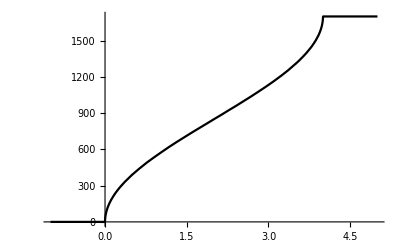

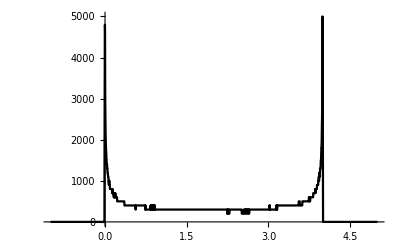

```mathematica
Plot[NLω[ω],{ω,-1,4 Subscript[ω, 0]^2+1},PlotPoints->45,MaxRecursion->6,PlotRange->All,PlotStyle->Black]
Plot[ρ[ω,0.01],{ω,-1,4 Subscript[ω, 0]^2+1},PlotPoints->45,MaxRecursion->6,PlotRange->All,PlotStyle->Black]
```

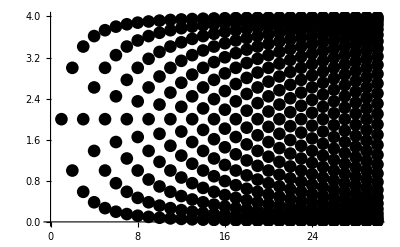

```mathematica
(* The distribution of the Eigenmodes of the matrix Dn *)
Show[Table[DiscretePlot[EigValSol[l],{n,l,l},Filling->None,PlotStyle->{Black},PlotMarkers->{"•",Medium}],{l,30}], PlotRange->{{0,30},{0,4}}]
```

### Investigation the relationship between (ω^2)_0 and (ω^2)_max .

Define (ω^2)_max to be the value of ω that the density of state will converge to zero afterwards , for lets take (ω^2)_0=1, lets observe the value of  (ω^2)_max_

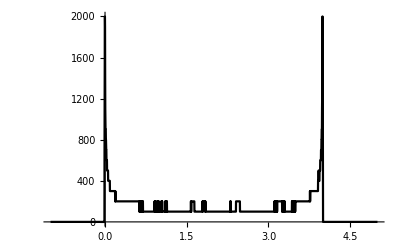

```mathematica
Subscript[ω, 0]=1;
ListOfSol=EigValSol[700];
Plot[ρ[ω,0.01],{ω,-1,5},PlotPoints->45,MaxRecursion->6,PlotRange->All,PlotStyle->Black]
```

The value of (ω^2)_max for ω_0=1 was (ω^2)_max=4, Now we will take ω_0=2->(ω^2)_0=4, and we will observe (ω^2)_max

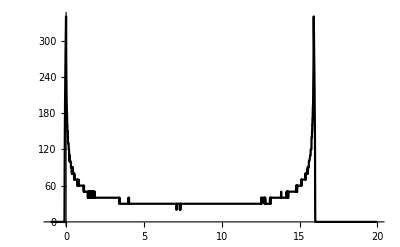

```mathematica
Subscript[ω, 0]=2;
ListOfSol=EigValSol[700];
Plot[ρ[ω,0.1],{ω,-1,20},PlotPoints->45,MaxRecursion->6,PlotRange->All,PlotStyle->Black]
```

The value of (ω^2)_max for ω_0=2 was (ω^2)_max=16, Now we will take ω_0=3->(ω^2)_0=9, and we will observe (ω^2)_max

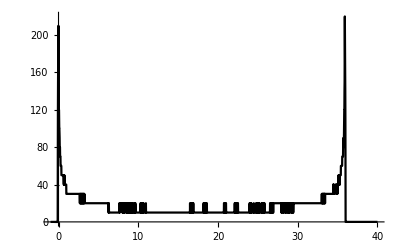

```mathematica
Subscript[ω, 0]=3;
ListOfSol=EigValSol[700];
Plot[ρ[ω,0.1],{ω,-1,40},PlotPoints->45,MaxRecursion->6,PlotRange->All,PlotStyle->Black]
```

The value of (ω^2)_max for ω_0=3 was (ω^2)_max=36, We can now describe the relationship between (ω^2)_max and (ω^2)_0 by this empirical formula: (ω^2)_max=4(ω^2)_0, we can verify it by choosing a value of (ω^2)_0 then predict the value of ((ω^2)_max)^and check if we were accurate. Lets take ω_0=5->(ω^2)_0=25, we predict (ω^2)_max to be 100:

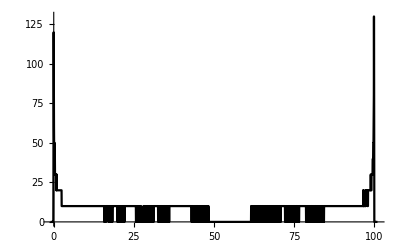

```mathematica
Subscript[ω, 0]=5;
ListOfSol=EigValSol[700];
Plot[ρ[ω,0.1],{ω,-1,4 Subscript[ω, 0]^2+1},PlotPoints->45,MaxRecursion->6,PlotRange->All,PlotStyle->Black]
```

### The empirical formula (ω^2)_max=4(ω^2)_0 appears to work fine for this system of atoms.